# Some rule properties (version 06-10-2022)

## Number conserving rules (conservative, for short)

### k = 2, r = 1

```mathematica
Select[Range[0,2^(2^3)-1],BFConservativeQ[#,2,1]&]
```

{170,184,204,226,240}

```mathematica
GraphicsGrid[{Module[{ic=RandomInteger[{0,1},100],rule=#},
ListPlot[
{Count[#,0]&/@CellularAutomaton[{rule,2,1},ic,100],
Count[#,1]&/@CellularAutomaton[{rule,2,1},ic,100]},
PlotLabels->{0,1},PlotLabel->"Rule "<>ToString[rule]
]]&/@{170,184,204,226,240}}]
```

-Graphics-

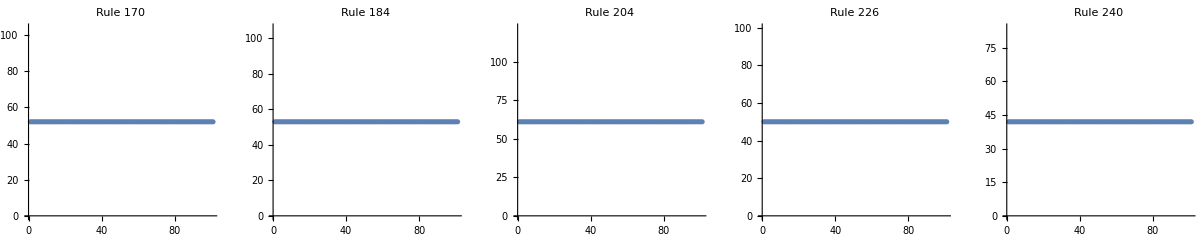

```mathematica
GraphicsGrid[{Module[{ic=RandomInteger[{0,1},100],rule=#},
ListPlot[
Total/@CellularAutomaton[{rule,2,1},ic,100],PlotLabel->"Rule "<>ToString[rule]
]]&/@{170,184,204,226,240}}]
```

```mathematica
Module[{ic=RandomInteger[{0,1},100]},
Print[If[Count[ic,1]>50,"#1s > #0s",If[Count[ic,0]>50,"#0s > #1s","#1s = #0s"]]];
ArrayPlot[CellularAutomaton[226,ic,100]]]
```

#1s > #0s

-Graphics-

```mathematica
Module[{ic=Join[Table[0,{25}],Table[1,{25}]]},
ArrayPlot[CellularAutomaton[226,ic,30]]]
```

-Graphics-

### k = 3, r = 0.5

```mathematica
Select[Range[0,3^(3^2)-1],BFConservativeQ[#,3,0.5]&]
```

{15897,16641,18561,19305}

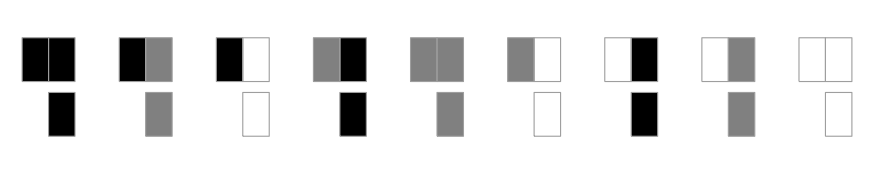

```mathematica
RulePlot[CellularAutomaton[{15897,3,1/2}]]
```

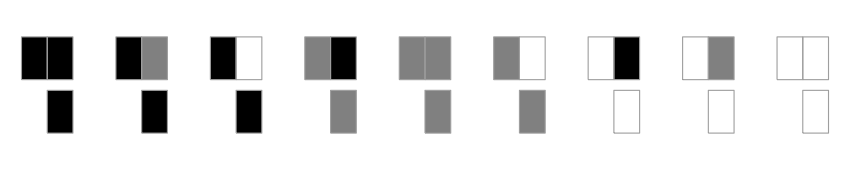

```mathematica
RulePlot[CellularAutomaton[{19305,3,1/2}]]
```

```mathematica
GraphicsGrid[{Module[{ic=RandomInteger[{0,2},100],rule=#},
ListPlot[
{Count[#,0]&/@CellularAutomaton[{rule,3,FlexRadius[0.5]},ic,150],
Count[#,1]&/@CellularAutomaton[{rule,3,FlexRadius[0.5]},ic,150],
Count[#,2]&/@CellularAutomaton[{rule,3,FlexRadius[0.5]},ic,150]},
PlotLabels->{0,1,2},PlotLabel->"Rule "<>ToString[rule]
]]&/@{15897,16641,18561,19305}}]
```

-Graphics-

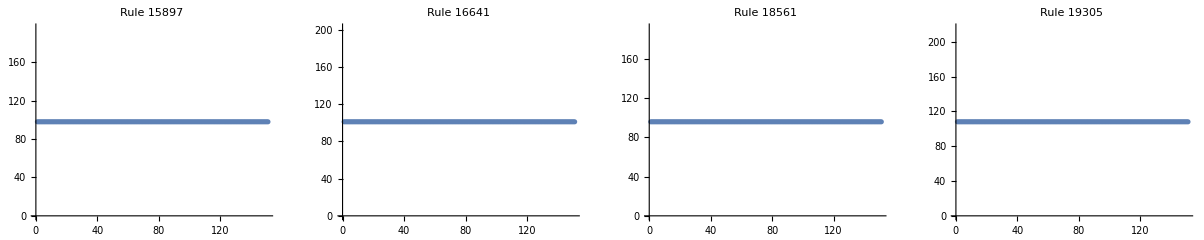

```mathematica
GraphicsGrid[{Module[{ic=RandomInteger[{0,2},100],rule=#},
ListPlot[
Total/@CellularAutomaton[{rule,3,FlexRadius[0.5]},ic,150],PlotLabel->"Rule "<>ToString[rule]
]]&/@{15897,16641,18561,19305}}]
```

### Question 1: Which are the strictly number conserving rules (i.e., those which always preserve the individual number of cells in every state at each iteration) with k = 3, r = 0.5?

1) Notice that if a rule is strictly number conserving, then it is also number conserving (but not necessarily the opposite). So, strictly number conserving rules is a subset of the number conserving ones.
2) The 4 number conserving rules of the space shown above are the identity, the shift-right and 2 others. While the former 2 are (trivial) strictly number conserving rules, the latter 2 are not, as shown in the plots.
So: with with k = 3, r = 0.5, only the identity and the shift-right rules are strictly number conserving rules.

### Question 2 (open): How could strict number conservation be characterised in general?

## Reversible rules

### k = 2, r = 1

```mathematica
Select[Range[0,2^(2^3)-1],ReversibleRuleQ[#,2,1]&]
```

{15,51,85,170,204,240}

```mathematica
GatherBy[{15,51,85,170,204,240},Sort@DynamicalEquivalenceClass[#]&]//MatrixForm
```

({15,85}
{51}
{170,240}
{204})

```mathematica
{#, InverseRule[#]}&/@%%//MatrixForm
```

(15 | {85,2,1}
51 | {51,2,1}
85 | {15,2,1}
170 | {240,2,1}
204 | {204,2,1}
240 | {170,2,1})

```mathematica
InverseRule[15]
```

{85,2,1}

```mathematica
First/@GatherBy[{#,2,1}&/@{15,51,85,170,204,240},Sort@DynamicalEquivalenceClass[Sequence@@#]&]
```

{{15,2,1},{51,2,1},{170,2,1},{204,2,1}}

```mathematica
{#,RuleMinDNF[#,1]}&/@(First/@%)//MatrixForm
```

(15 | (!x)_-1
51 | (!x)_0
170 | x_1
204 | x_0)

### k = 2, r = 1.5

```mathematica
Select[Range[0,2^(2^4)-1],ReversibleRuleQ[#,2,1.5]&]
```

{255,3855,3915,11535,13107,13155,14643,21845,43690,50892,52380,52428,54000,61620,61680,65280}

```mathematica
GatherBy[{#,2,1.5}&/@%,Sort@DynamicalEquivalenceClass[Sequence@@#]&]//MatrixForm
```

({{255,2,1.5},{21845,2,1.5}}
{{3855,2,1.5},{13107,2,1.5}}
{{3915,2,1.5},{11535,2,1.5},{13155,2,1.5},{14643,2,1.5}}
{{43690,2,1.5},{65280,2,1.5}}
{{50892,2,1.5},{52380,2,1.5},{54000,2,1.5},{61620,2,1.5}}
{{52428,2,1.5},{61680,2,1.5}})

```mathematica
First/@GatherBy[{#,2,1.5}&/@{255,3855,3915,11535,13107,13155,14643,21845,43690,50892,52380,52428,54000,61620,61680,65280},Sort@DynamicalEquivalenceClass[Sequence@@#]&]
```

{{255,2,1.5},{3855,2,1.5},{3915,2,1.5},{43690,2,1.5},{50892,2,1.5},{52428,2,1.5}}

```mathematica
GraphicsRow[Module[{ic=RandomInteger[{0,1},100]},ArrayPlot[CellularAutomaton[{First@#,2,FlexRadius[1.5]},ic,150],PlotLabel->#]&/@%]]
```

-Graphics-

```mathematica
{#,RuleMinDNF[#,1.5]}&/@(First/@{{255,2,1.5},{3855,2,1.5},{3915,2,1.5},{43690,2,1.5},{50892,2,1.5},{52428,2,1.5}})//MatrixForm
```

(255 | (!x)_-2
3855 | (!x)_-1
3915 | (x_-2&&(!x)_-1)||((!x)_-2&&x_-1&&x_0&&(!x)_1)||((!x)_-1&&(!x)_0)||((!x)_-1&&x_1)
43690 | x_1
50892 | (x_-2&&(!x)_-1&&(!x)_0&&x_1)||((!x)_-2&&x_0)||(x_-1&&x_0)||(x_0&&(!x)_1)
52428 | x_0)

```mathematica
{#, InverseRule[Sequence@@#]}&/@{{255,2,1.5},{3855,2,1.5},{3915,2,1.5},{43690,2,1.5},{50892,2,1.5},{52428,2,1.5}}//MatrixForm
```

$Aborted

```mathematica
InverseRule[3915,2,1.5]
```

$Aborted

### k = 3, r = 0.5

```mathematica
Select[Range[0,3^(3^2)-1],ReversibleRuleQ[#,3,0.5]&]
```

{377,481,611,715,1079,2119,2899,3785,3791,3841,4217,4745,5243,5299,5311,5515,7995,8321,8327,8439,8543,8801,9503,9711,9971,10179,10881,11139,11243,11355,11361,11687,14167,14371,14383,14439,14937,15465,15841,15891,15897,16783,17563,18603,18967,19071,19201,19305}

```mathematica
First/@GatherBy[{#,3,0.5}&/@%,Sort@DynamicalEquivalenceClass[Sequence@@#]&]
```

{{377,3,0.5},{481,3,0.5},{611,3,0.5},{715,3,0.5},{4217,3,0.5},{14439,3,0.5},{15897,3,0.5}}

```mathematica
GraphicsRow[Module[{ic=RandomInteger[{0,1},100]},ArrayPlot[CellularAutomaton[{First@#,3,FlexRadius[0.5]},ic,150],PlotLabel->#]&/@%]]
```

-Graphics-

```mathematica
{#,RuleMinDNF[#,0.5]}&/@(First/@{{377,3,0.5},{481,3,0.5},{611,3,0.5},{715,3,0.5},{4217,3,0.5},{14439,3,0.5},{15897,3,0.5}})//MatrixForm
```

(377 | (x_-1&&x_0)||((!x)_-1&&(!x)_0)
481 | (!x)_-1&&(!x)_0
611 | (!x)_-1
715 | (!x)_-1||x_0
4217 | (x_-1&&x_0)||((!x)_-1&&(!x)_0)
14439 | (!x)_-1||(!x)_0
15897 | (x_-1&&x_0)||((!x)_-1&&(!x)_0))

```mathematica
{#, InverseRule[Sequence@@#]}&/@{{377,3,0.5},{481,3,0.5},{611,3,0.5},{715,3,0.5},{4217,3,0.5},{14439,3,0.5},{15897,3,0.5}}//MatrixForm
```

$Aborted

```mathematica
{{481,611},{4217,14439,15897}}
```

```mathematica
InverseRule[715,3,0.5]
InverseRule[Sequence@@%]
```

{3226214320571,3,1}

{387410647,3,1}

```mathematica
ReduceRuleRadius[{387410647,3,1}]
ExtendRuleRadius[{715,3,0.5},1]
```

{715,3,0.5}

{387410647,3,1}

## Captive and Spreading State rules

### Captive rules

```mathematica
Select[Range[0,255],CaptiveQ]
```

{128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198,200,202,204,206,208,210,212,214,216,218,220,222,224,226,228,230,232,234,236,238,240,242,244,246,248,250,252,254}

```mathematica
%//Length
```

64

```mathematica
Union@Flatten[RuleTable[#]&/@%%,1]//MatrixForm
```

({0,0,0} | 0
{0,0,1} | 0
{0,0,1} | 1
{0,1,0} | 0
{0,1,0} | 1
{0,1,1} | 0
{0,1,1} | 1
{1,0,0} | 0
{1,0,0} | 1
{1,0,1} | 0
{1,0,1} | 1
{1,1,0} | 0
{1,1,0} | 1
{1,1,1} | 1)

### Rules with a Spreading State

```mathematica
Select[Range[0,255],SpreadingStateQ]
```

{128,254}

```mathematica
MatrixForm/@(RuleTable[#]&/@{128,254})
```

{({1,1,1} | 1
{1,1,0} | 0
{1,0,1} | 0
{1,0,0} | 0
{0,1,1} | 0
{0,1,0} | 0
{0,0,1} | 0
{0,0,0} | 0),({1,1,1} | 1
{1,1,0} | 1
{1,0,1} | 1
{1,0,0} | 1
{0,1,1} | 1
{0,1,0} | 1
{0,0,1} | 1
{0,0,0} | 0)}

## Totalistic and Outer-Totalistic rules

### More details:

Wolfram Mathworld: Totalistic CellularAutomata
Wolfram Mathworld: Outer-Totalistic CellularAutomata

### Totalistic rules: Defined in terms of the ‘average’ state in the neighbourhood

```mathematica
RulePlot[CellularAutomaton[232]]
```

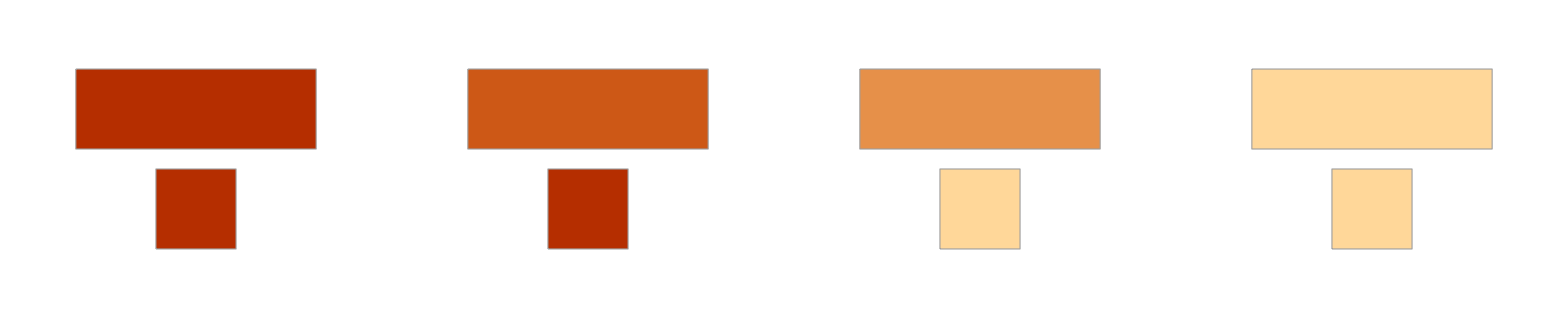

```mathematica
(* Colours represent the average value (or the sum) of the three states of the neighbourhood. *)
RulePlot[CellularAutomaton[{12,{2,1}}],PlotTheme->"VibrantColor"]
```

```mathematica
Select[Range[0,255],TotalisticQ]
%//Length
GatherBy[%%,Sort@DynamicalEquivalenceClass[#]&]
```

{0,1,22,23,104,105,126,127,128,129,150,151,232,233,254,255}

16

{{0,255},{1,127},{22,151},{23},{104,233},{105},{126,129},{128,254},{150},{232}}

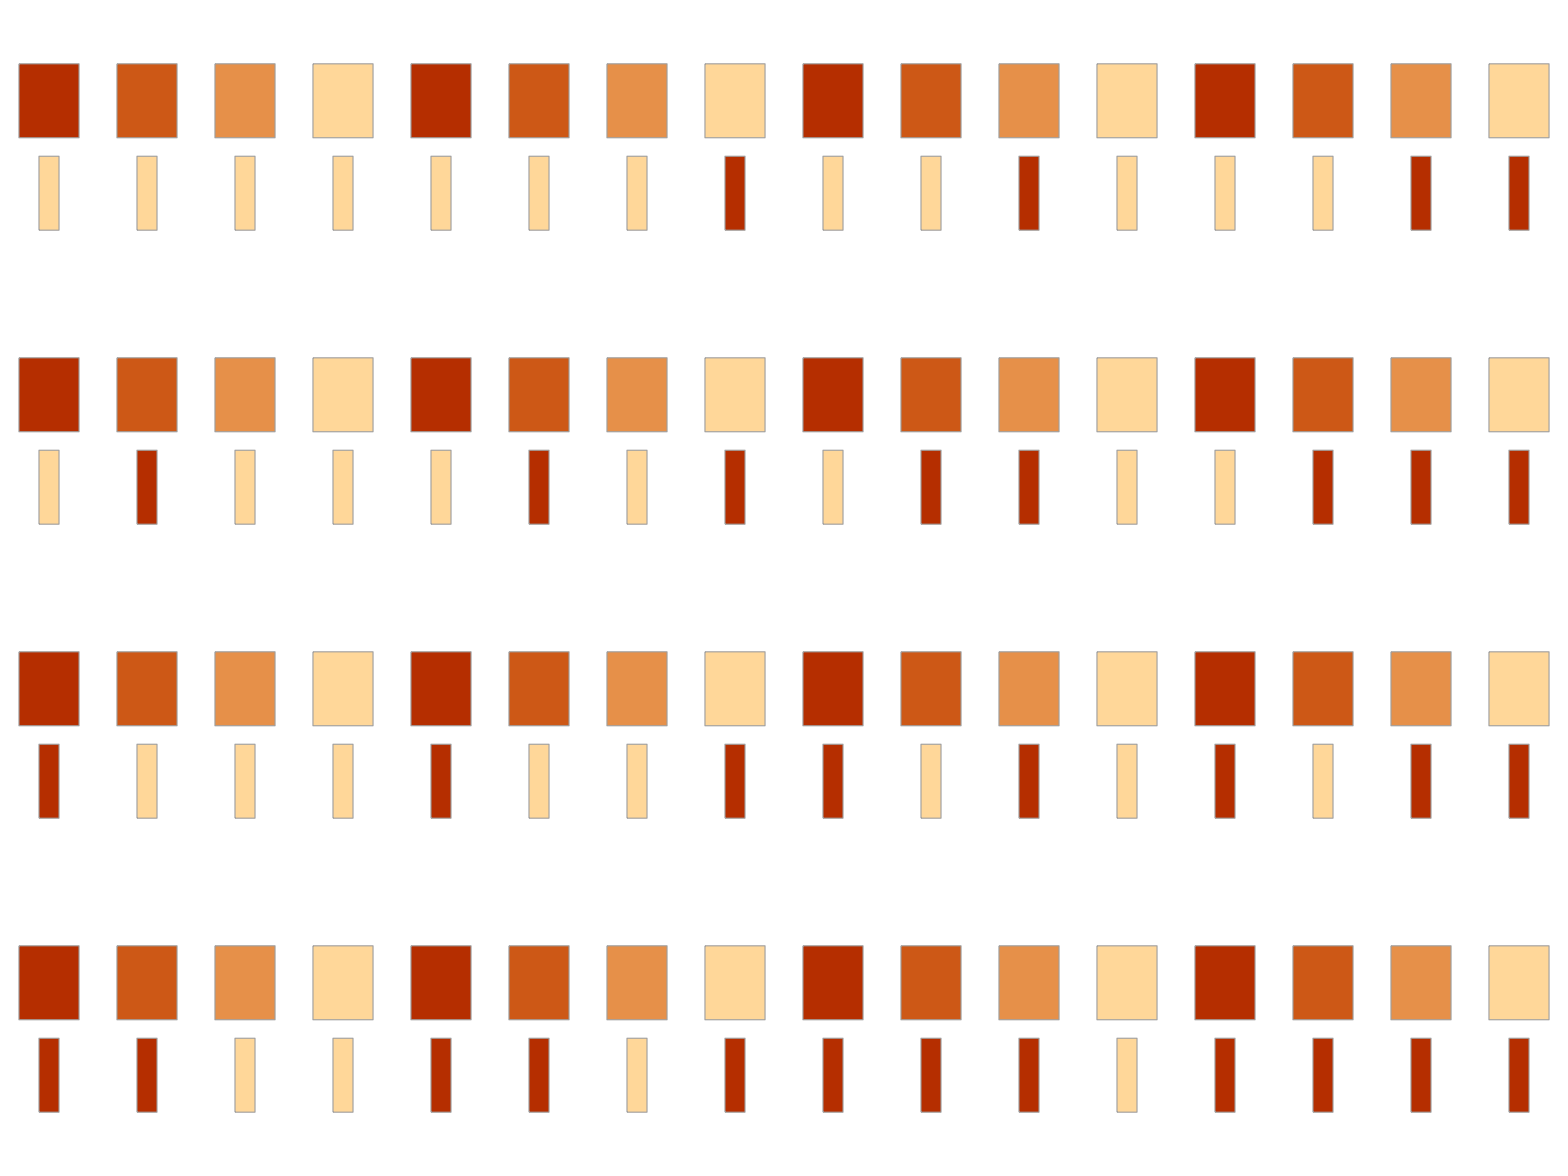

```mathematica
Partition[RulePlot[CellularAutomaton[{#,{2,1}}],PlotTheme->"VibrantColor"]&/@Range[0,15],4]//Grid
```

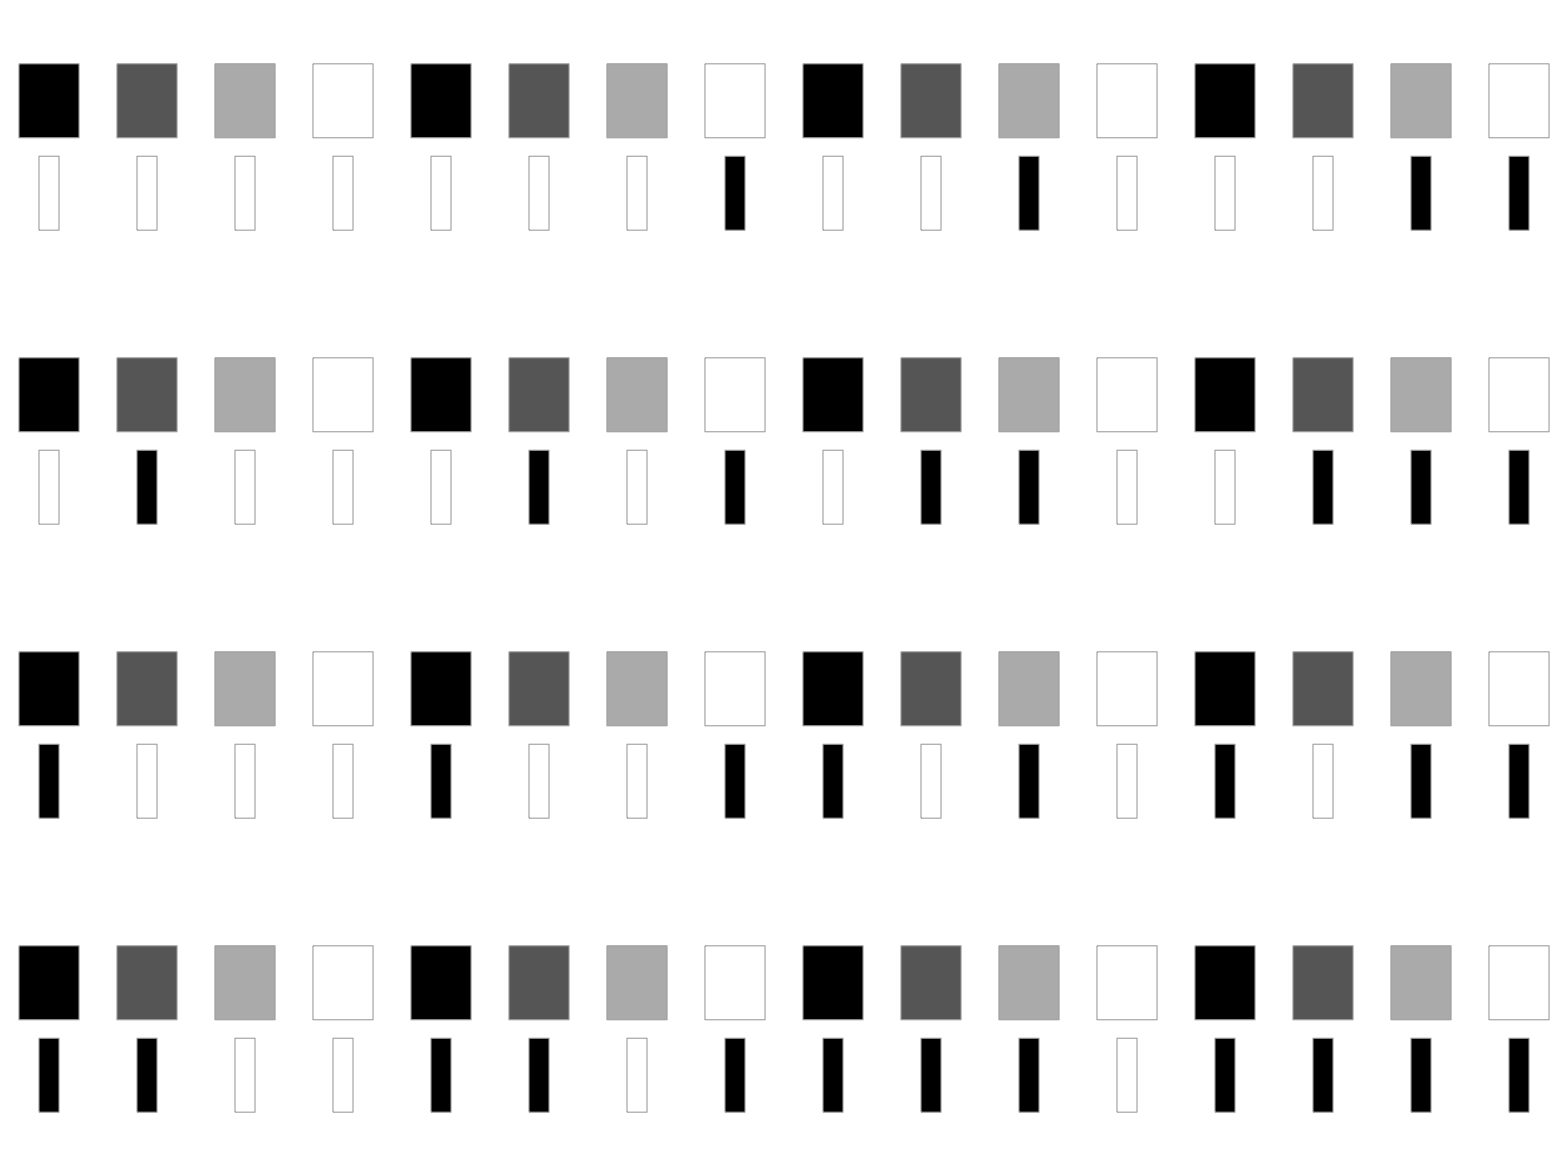

```mathematica
Partition[RulePlot[CellularAutomaton[{#,{2,1}}]]&/@Range[0,15],4]//Grid
```

### Outer-totalistic rules: Defined in terms of the state of the central cell and the ‘average’ state of its neighbouring cells

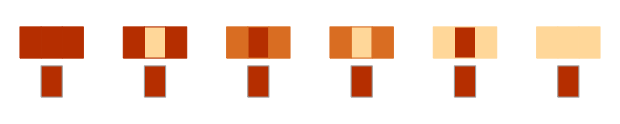

```mathematica
(* Colours represent the average value (or the sum) of the two side states of the neighbourhood. *)
RulePlot[CellularAutomaton[{63,{2,{2,1,2}}}],PlotTheme->"VibrantColor"]
```

```mathematica
Select[Range[0,255],OuterTotalisticQ]
%//Length
GatherBy[%%,Sort@DynamicalEquivalenceClass[#]&]
```

{0,1,4,5,18,19,22,23,32,33,36,37,50,51,54,55,72,73,76,77,90,91,94,95,104,105,108,109,122,123,126,127,128,129,132,133,146,147,150,151,160,161,164,165,178,179,182,183,200,201,204,205,218,219,222,223,232,233,236,237,250,251,254,255}

64

{{0,255},{1,127},{4,223},{5,95},{18,183},{19,55},{22,151},{23},{32,251},{33,123},{36,219},{37,91},{50,179},{51},{54,147},{72,237},{73,109},{76,205},{77},{90,165},{94,133},{104,233},{105},{108,201},{122,161},{126,129},{128,254},{132,222},{146,182},{150},{160,250},{164,218},{178},{200,236},{204},{232}}

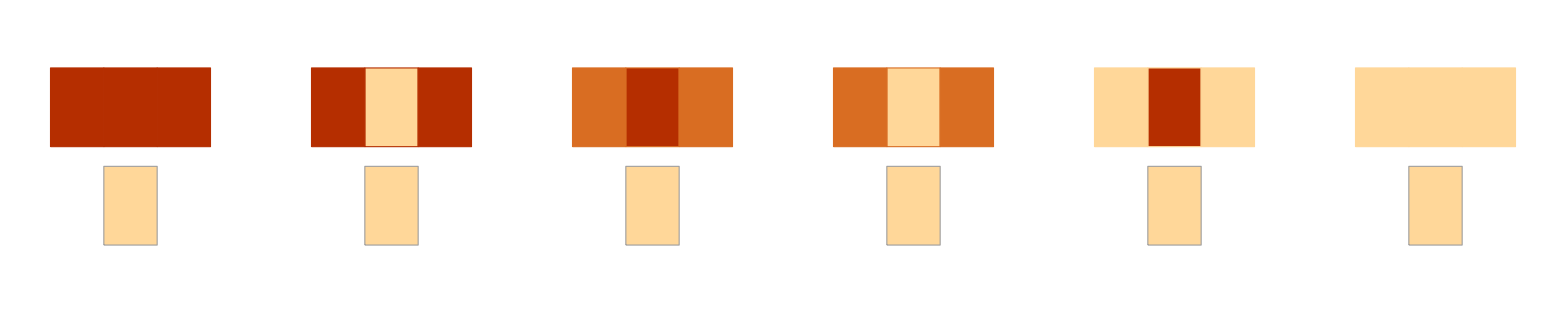
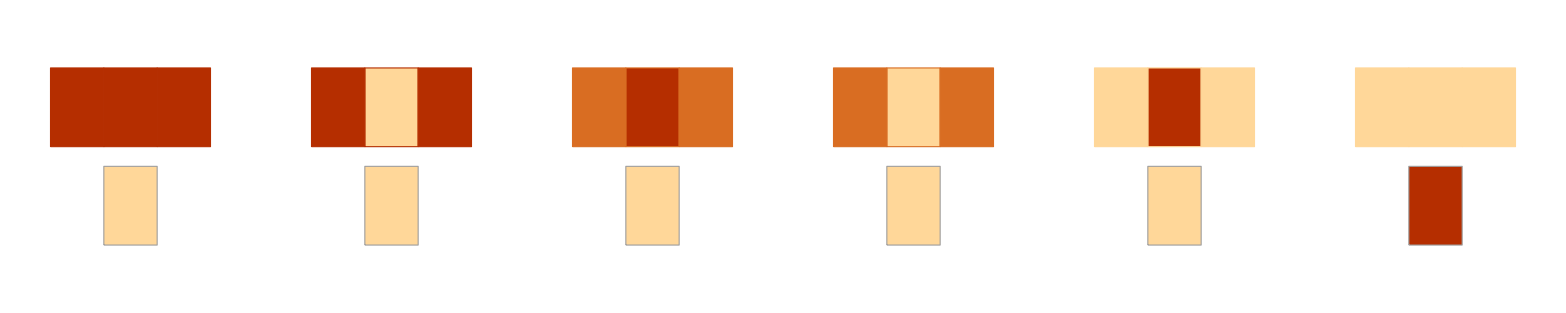
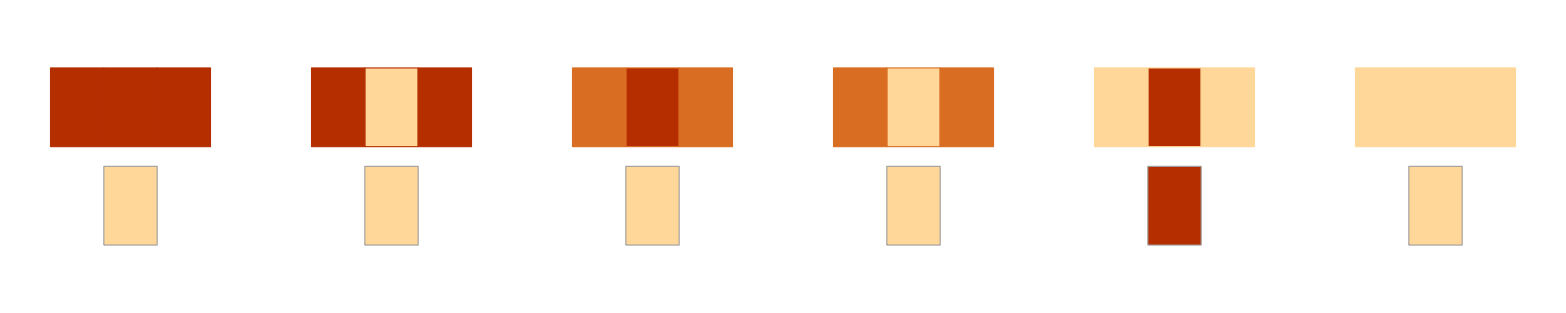
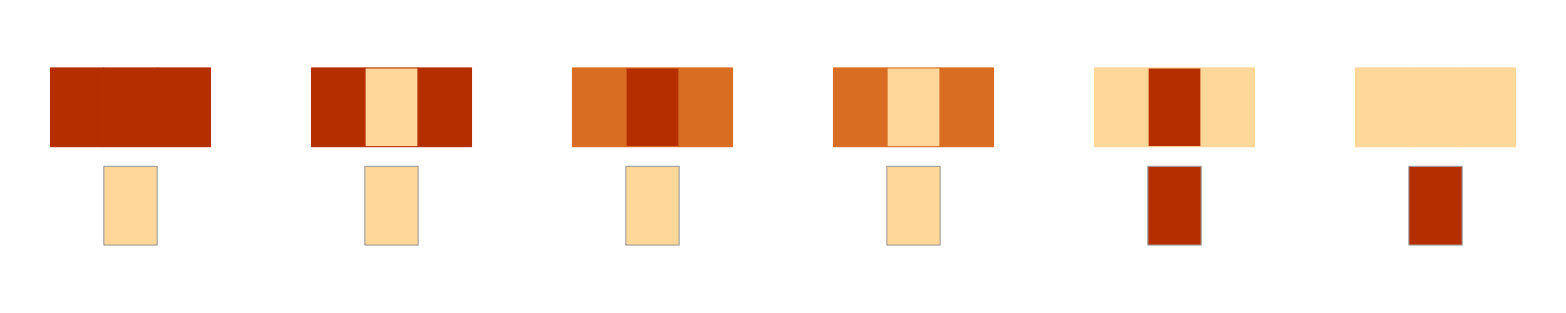
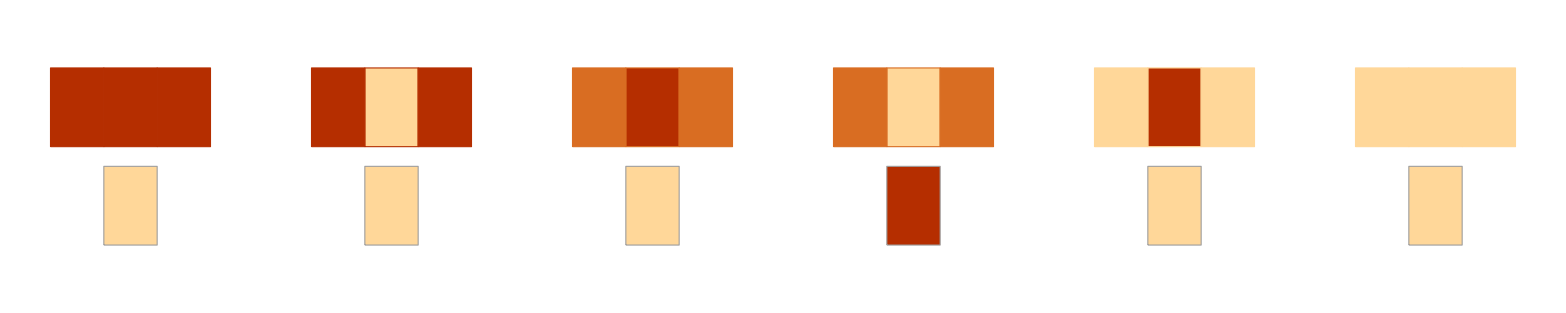
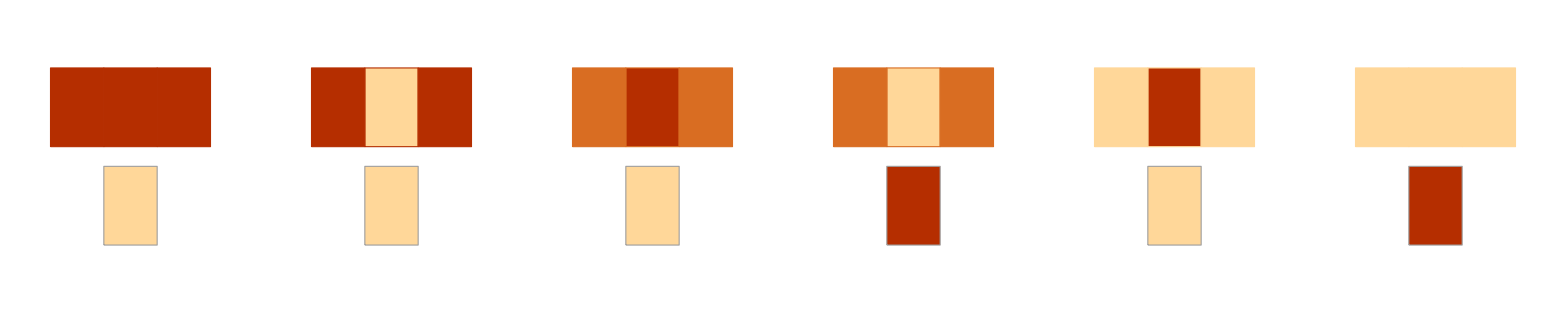
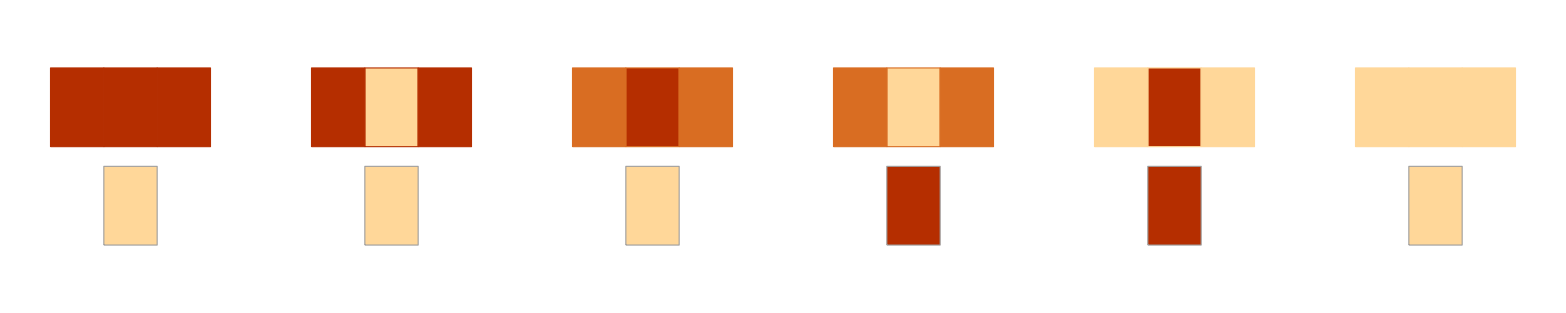
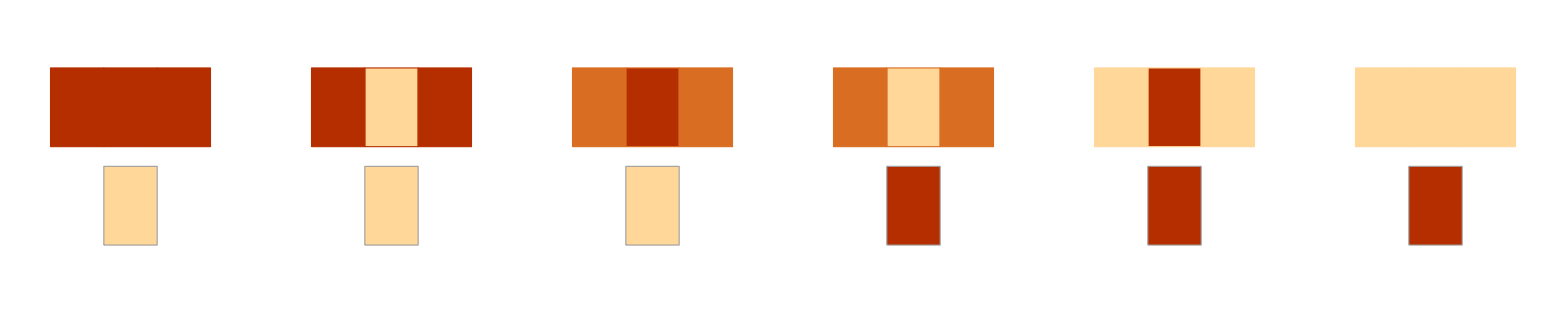
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Partition[RulePlot[CellularAutomaton[{#,{2,{2,1,2}}}],PlotTheme->"VibrantColor"]&/@Range[0,63],3]//Grid
```

### Every totalistic rule is also outer-totalistic

```mathematica
Select[Range[0,255],TotalisticQ]
```

{0,1,22,23,104,105,126,127,128,129,150,151,232,233,254,255}

```mathematica
Select[Range[0,255],(OuterTotalisticQ[#]∧TotalisticQ[#])&]
```

{0,1,22,23,104,105,126,127,128,129,150,151,232,233,254,255}

### Number of totalistic and outer-totalistic rules

### Implementation of totalistic and outer-totalistic rules (and ECAs) with weights, in the CellularAutomaton function

#### More detail in :

http://mathematica.stackexchange.com/questions/111558/notation-for-2d-semitotalistic-9-neighbor-moore-cellular-automata

#### ECAs can be implemented with weights 4, 2 and 1

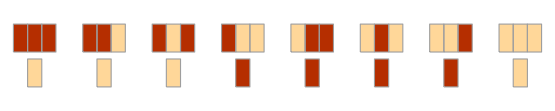

```mathematica
RulePlot[CellularAutomaton[30],PlotTheme->"VibrantColor"]
```

```mathematica
CellularAutomaton[  30,                                           {{1},0},50]===
CellularAutomaton[{30,2,1},                            {{1},0},50]===
CellularAutomaton[{30,{2,{4,2,1}}},      {{1},0},50]===
CellularAutomaton[{30,{2,{4,2,1}},1},{{1},0},50]
```

True

```mathematica
RulePlot[CellularAutomaton[30]]
```

4-2-1      4-2          4----1       4                   2-1         2                  1             0

-Graphics-

#### 2D Totalistic

```mathematica
Moore:              {n,{k,1},                                                                    {1,1}}
Moore:              {n,{k,{{1,1,1},{1,1,1},{1,1,1}}},{1,1}}
von Neumann:  {n,{k,{{0,1,0},{1,1,1},{0,1,0}}},{1,1}}
```

```mathematica
CellularAutomaton[{14,{2,1},                                                                    {1,1}},{{{1}},0},100]===CellularAutomaton[{14,{2,{{1,1,1},{1,1,1},{1,1,1}}},{1,1}},{{{1}},0},100]
```

True

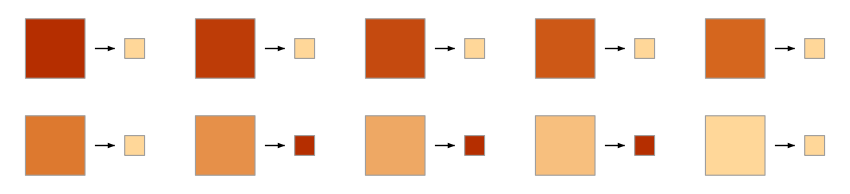

```mathematica
RulePlot[CellularAutomaton[{14, {2, 1}, {1, 1}}],PlotTheme->"VibrantColor"]
```

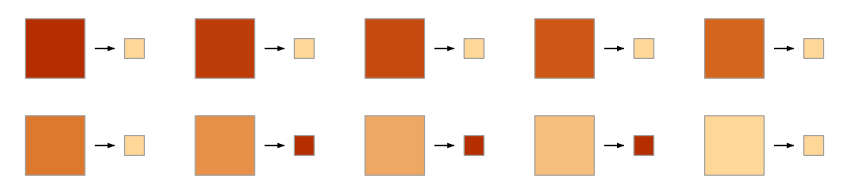

```mathematica
RulePlot[CellularAutomaton[{14,{2,{{1,1,1},{1,1,1},{1,1,1}}},{1,1}}],PlotTheme->"VibrantColor"]
```

```mathematica
FromDigits[{0,0,0,0,0,0,1,1,1,0},2]
```

14

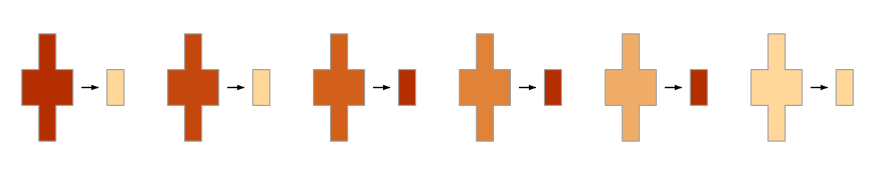

```mathematica
RulePlot[CellularAutomaton[{14, {2, {{0,1,0},{1,1,1},{0,1,0}}}, {1, 1}}],PlotTheme->"VibrantColor"]
```

```mathematica
FromDigits[{0,0,0,1,1,1,0},2]
```

14

#### 2D Outer-Totalistic

```mathematica
Moore:             {n,{k,{{k,k,k},{k,1,k},{k,k,k}}},{1,1}}
von Neumann: {n,{k,{{0,k,0},{k,1,k},{0,k,0}}},{1,1}}
```

```mathematica
GameOfLife={224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
```

```mathematica
Puffer={{1,4},{2,5},{3,1},{3,5},{4,2},{4,3},{4,4},{4,5},{8,1},{9,2},{9,3},{10,3},{11,3},{12,2},{15,1},{15,4},{16,5},{17,1},{17,5},{18,2},{18,3},{18,4},{18,5}}
```

{{1,4},{2,5},{3,1},{3,5},{4,2},{4,3},{4,4},{4,5},{8,1},{9,2},{9,3},{10,3},{11,3},{12,2},{15,1},{15,4},{16,5},{17,1},{17,5},{18,2},{18,3},{18,4},{18,5}}

(1 | 1 | 1
1 | 0 | 1
1 | 1 | 1)≠(2 | 2 | 2
2 | 1 | 2
2 | 2 | 2)

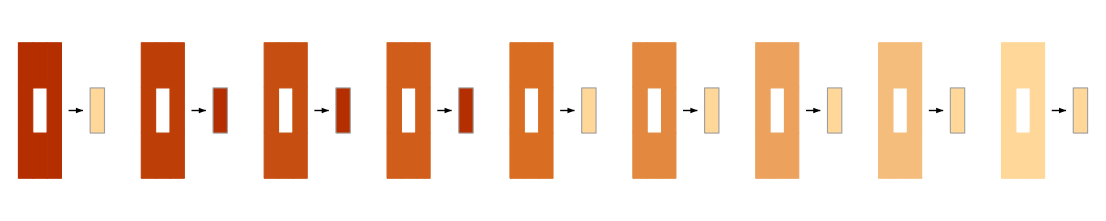

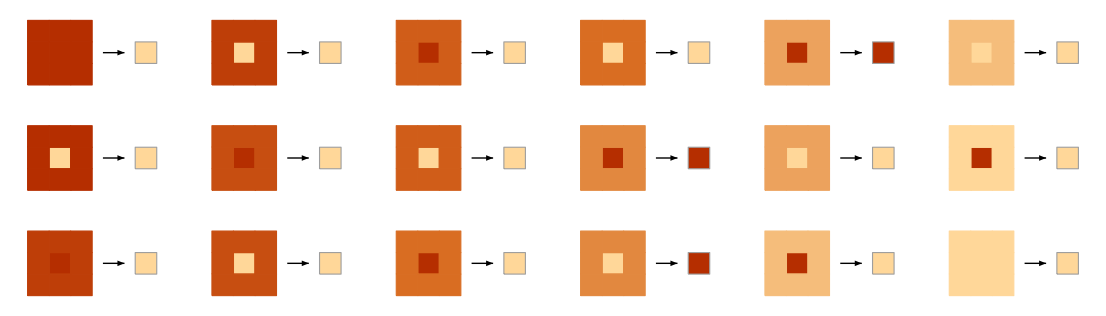

```mathematica
RulePlot[CellularAutomaton[{224,{2,{{1,1,1},{1,0,1},{1,1,1}}},{1,1}}],PlotTheme->"VibrantColor"]
RulePlot[CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}}],PlotTheme->"VibrantColor"]
```

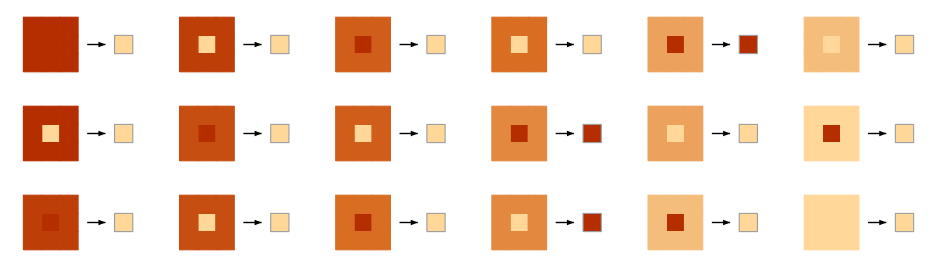

```mathematica
RulePlot[CellularAutomaton[GameOfLife],PlotTheme->"VibrantColor"]
```